NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 845.328.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 844.268.

NDSolve::mxst: Maximum number of 100000 steps reached at the point t == 842.984.

General::stop: Further output of NDSolve::mxst will be suppressed during this calculation.

NDSolve`ProcessSolutions::nodata: No solution data was computed between t == 800. and t == 850..

General::stop: Further output of NDSolve`ProcessSolutions::nodata will be suppressed during this calculation.

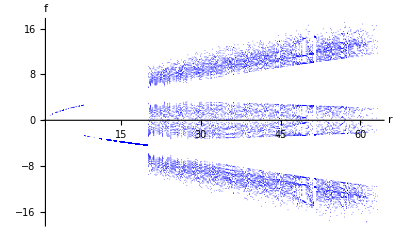

```mathematica
ecf=s (p[t]-f[t]);
ecp=-p[t]+d[t] f[t];
ecd=b (r-d[t]-f[t] p[t]);

par={s->3.,b->1,r->100};
t0=800;
tf=850;



estables[ra_]:=Module[{par,solnum,points},par={s->3.,b->1,r->ra};
{solnum,points}=Reap@NDSolve[{Derivative[1][f][t]==ecf,Derivative[1][p][t]==ecp,Derivative[1][d][t]==ecd,f[0]==0.00001,p[0]==0.,d[0]==1,WhenEvent[{f'[t]==0&&t>t0},Sow[f[t]]]}/.par,{f,p,d},{t,t0,tf},MaxSteps->100000];
Flatten[points]];


r0=0;
rf=105;
dr=0.2;

ys=Table[{ra,e},{ra,r0,rf,dr},{e,estables[ra]}];
ListPlot[Flatten[ys,1],PlotRange->All,DataRange->{r0,rf},PlotStyle->{Blue,PointSize[0.001]},Joined->False,AxesLabel->{r,f}]
```